## NLL Angularities with Shape Function

### Baseline Values

```mathematica
αsCR baseline=0.117998;(*0.1184;*)
NF baseline = 5;
R baseline  = 0.6;
Q baseline = 200.0 ;
Ω0 baseline = 0.350;  (*in GeV this number needs to be checked *)
Ω0 tiny = 0.00001; (* used for quasi-parton cross check *)
```

### Physical Constants

```mathematica
mZ=91.19;
β0=11/(4π)-5/(6π);
β1=153/(24 π^2)-75/(24 π^2)-20/(24 π^2);
K=(67/6-π^2/2)-25/9;
CF = 4/3;
CA = 3;
Bq =-3/4;
Bg[NF_]:=-(33-2NF)/36;
```

### Angularites: Perturbative Cumulative Distribution

```mathematica
AngularitiesMasterCumulative[τ1_, Cfactor_, Bfactor_,αsCR_,  R_, Q_, use2loop_, β_]:= Block[{L, αs,λ, r,T,Talt,dr,ANS, kt},

kt = Q* R /2.0; (* factor of two because jet energy is half of collision energy in e+e-*)
L=Log[1/τ1];
αs=(1/αsCR+23/(6π)Log[kt/mZ]+116/(92π)Log[1+23/(6π)αsCR Log[kt/mZ]])^-1;
λ=αs*β0*L;
r=L/(2π β0 λ(β-1))((1-2λ)Log[1-2λ]-(β-2λ)Log[1-(2λ)/β])+use2loop*1/(β-1)(K/(4 π^2 β0^2)(β Log[1-(2λ)/β]-Log[1-2λ])+β1/(2π β0^3)(Log[1-2λ]^2/2-β/2 Log[1-(2λ)/β]^2+Log[1-2λ]-β Log[1-(2λ)/β]));
T=-1/(π β0)Log[1-2λ];
Talt=-1/(π β0)Log[1-(2λ)/β];
dr=1/(β-1)(T-Talt);
ANS = ⅇ^(-EulerGamma Cfactor dr)/Gamma[1+Cfactor dr] ⅇ^(-Cfactor(r+Bfactor  Talt));
If[1-2λ>0 && 1-(2λ)/β>0 && αs>0,Evaluate[ANS],0.0]
]
```

### Defining Benchmarks

```mathematica
(* Baseline*)
AngularitiesCumulative[τ1_,"baseline","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R baseline, Q baseline, 1, β]
AngularitiesCumulative[τ1_,"baseline","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R baseline, Q baseline, 1,β]

(* No g -> qq , only gluon has to change *)
AngularitiesCumulative[τ1_,"nogqq","quark", β_]:=AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R baseline, Q baseline, 1,β]
AngularitiesCumulative[τ1_,"nogqq","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[0], αsCR baseline, R baseline, Q baseline, 1,β]

(* No 2loop effects *)
AngularitiesCumulative[τ1_,"no2loop","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R baseline, Q baseline, 0, β]
AngularitiesCumulative[τ1_,"no2loop","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R baseline, Q baseline, 0,β]

(* Q sweep*)
AngularitiesCumulative[τ1_,"Q=50","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R baseline, 50.0,1, β]
AngularitiesCumulative[τ1_,"Q=100","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R baseline, 100.0,1, β]
AngularitiesCumulative[τ1_,"Q=200","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R baseline, 200.0,1, β]
AngularitiesCumulative[τ1_,"Q=400","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R baseline, 400.0,1, β]
AngularitiesCumulative[τ1_,"Q=800","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R baseline, 800.0, 1,β]

AngularitiesCumulative[τ1_,"Q=50","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R baseline, 50.0, 1,β]
AngularitiesCumulative[τ1_,"Q=100","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R baseline, 100.0,1, β]
AngularitiesCumulative[τ1_,"Q=200","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R baseline, 200.0,1, β]
AngularitiesCumulative[τ1_,"Q=400","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R baseline, 400.0,1, β]
AngularitiesCumulative[τ1_,"Q=800","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R baseline, 800.0,1, β]

(* R sweep *)
AngularitiesCumulative[τ1_,"R=0.2","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, 0.2, Q baseline, 1,β]
AngularitiesCumulative[τ1_,"R=0.4","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, 0.4, Q baseline, 1,β]
AngularitiesCumulative[τ1_,"R=0.6","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, 0.6, Q baseline, 1,β]
AngularitiesCumulative[τ1_,"R=0.8","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, 0.8, Q baseline, 1,β]
AngularitiesCumulative[τ1_,"R=1.0","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, 1.0, Q baseline, 1,β]

AngularitiesCumulative[τ1_,"R=0.2","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, 0.2, Q baseline, 1,β]
AngularitiesCumulative[τ1_,"R=0.4","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, 0.4, Q baseline,1, β]
AngularitiesCumulative[τ1_,"R=0.6","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, 0.6, Q baseline, 1,β]
AngularitiesCumulative[τ1_,"R=0.8","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, 0.8, Q baseline,1, β]
AngularitiesCumulative[τ1_,"R=1.0","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, 1.0, Q baseline,1, β]

(* αs sweep *)
AngularitiesCumulative[τ1_,"α/α0=0.8","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 0.8*αsCR baseline, R baseline, Q baseline,1, β]
AngularitiesCumulative[τ1_,"α/α0=0.9","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 0.9*αsCR baseline, R baseline, Q baseline,1, β]
AngularitiesCumulative[τ1_,"α/α0=1.0","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 1*αsCR baseline, R baseline, Q baseline,1, β]
AngularitiesCumulative[τ1_,"α/α0=1.1","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 1.1*αsCR baseline, R baseline, Q baseline,1, β]
AngularitiesCumulative[τ1_,"α/α0=1.2","quark", β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 1.2*αsCR baseline, R baseline, Q baseline,1, β]

AngularitiesCumulative[τ1_,"α/α0=0.8","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 0.8*αsCR baseline, R baseline, Q baseline, 1,β]
AngularitiesCumulative[τ1_,"α/α0=0.9","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 0.9*αsCR baseline, R baseline, Q baseline,1, β]
AngularitiesCumulative[τ1_,"α/α0=1.0","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 1*αsCR baseline, R baseline, Q baseline,1, β]
AngularitiesCumulative[τ1_,"α/α0=1.1","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 1.1*αsCR baseline, R baseline, Q baseline,1, β]
AngularitiesCumulative[τ1_,"α/α0=1.2","gluon", β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 1.2*αsCR baseline, R baseline, Q baseline,1, β]
```

### Angularities: Perturbative Differential Distribution and Lists/Interpolations

```mathematica
Needs["NumericalCalculus`"]

(* defining generic parton-level*)

Clear[AngularitiesDifferentialList, AngularitiesDifferentialInterpolation]

(* Have to start with zero for this to work*)
τ1max = 1.0;
τ1nbins = 1000;
τ1diff = τ1max/τ1nbins;
τ1order = 1;

AngularitiesDifferentialList[ "parton",para_, sample_, β_]:=  AngularitiesDifferentialList[ "parton", para, sample, β] =Block[{cumlist, cumlistL, cumlistR, centers, derivs},
cumlist = Table[{τ1,Max[Re[AngularitiesCumulative[τ1 , para, sample, β]],0.0]}, {τ1,τ1diff/2.0,τ1max-τ1diff/2.0,τ1diff}]; 
cumlistL = Rest[cumlist];
cumlistR = Most[cumlist];

centers = (cumlistL[[All,1]] + cumlistR[[All,1]])/2;
derivs = (cumlistL[[All,2]] - cumlistR[[All,2]])/τ1diff;
derivs =  Max[#,0.0]&/@ derivs;
derivs = derivs/Total[derivs]/τ1diff;
Join[{{0,0}}, Transpose[{centers,derivs}] ,{{τ1max,0}}]
]

AngularitiesDifferentialInterpolation[type_, para_, sample_, β_]:= AngularitiesDifferentialInterpolation[type, para, sample, β] = Interpolation[AngularitiesDifferentialList[type, para, sample, β], InterpolationOrder->τ1order]
```

### Non-perturbative Corrections

```mathematica
(*GenericShapeFunction[δ_, δ0_]:= (4δ)/δ0^2 ⅇ^(-(2δ)/δ0)*)
GenericShapeCumulative[δ_,δ0_]:= (δ0-ⅇ^(-(2 δ)/δ0) (2 δ+δ0))/δ0;

(* Dividing by 2 since Q is collision energy, but power correction is related to jet energy *)
AngularitiesNonPerturbativeShift[Ω0_,Q_, β_]:= (Ω0/(Q/2.0) - (Ω0/(Q/2.0))^β)/(β - 1);

Q of[_]:= Q baseline;
Q of["Q=50"]:= 50;
Q of["Q=100"]:= 100;
Q of["Q=200"]:= 200;
Q of["Q=400"]:= 400;
Q of["Q=800"]:= 800;

Ω0 of["quark"]:= Ω0 baseline
Ω0 of["gluon"]:= (CA/CF)*Ω0 baseline;

ShapeCumulative[δ_,"hadron",para_, sample_, β_]:= GenericShapeCumulative[δ,AngularitiesNonPerturbativeShift[Ω0 of[sample],Q of[para], β]]
ShapeCumulative[δ_,"quasi-parton",para_, sample_, β_]:= GenericShapeCumulative[δ,AngularitiesNonPerturbativeShift[Ω0 tiny,Q of[para], β]]

Clear[ShapeDifferentialList]

ShapeDifferentialList[type_,para_, sample_, β_]:=  ShapeDifferentialList[type, para, sample, β] =Block[{cumlist, cumlistL, cumlistR, centers, derivs},
cumlist = Table[{τ1,Max[Re[ShapeCumulative[τ1 ,type, para, sample, β]],0.0]}, {τ1,τ1diff/2.0,τ1max-τ1diff/2.0,τ1diff}]; 
cumlistL = Rest[cumlist];
cumlistR = Most[cumlist];

centers = (cumlistL[[All,1]] + cumlistR[[All,1]])/2;
derivs = (cumlistL[[All,2]] - cumlistR[[All,2]])/τ1diff;
(* next two steps probably aren't needed, but putting in anyways *)
derivs =  Max[#,0.0]&/@ derivs;
derivs = derivs/Total[derivs]/τ1diff;
Join[{{0,0}}, Transpose[{centers,derivs}] ,{{τ1max,0}}]
]


(* This technique only works if parton and shape have the same length, parton and shape have zero entries at 0, and equally spaced yada yada *)
AngularitiesDifferentialList[ type_,para_, sample_, β_]:=  AngularitiesDifferentialList[ type, para, sample, β]  = Block[{parton, shape,coords, values, total, shifted},
parton = AngularitiesDifferentialList[ "parton", para, sample, β];
shape = ShapeDifferentialList[type, para, sample, β];

(* This technique only works if parton and shape have the same length, parton and shape have zero entries at 0, and equally spaced yada yada *)
coords = parton[[All,1]];
values =  parton[[All,2]];

total = Table[0, {k,1, Length[parton]}];

For[i=1, i < Length[shape], i++,
total += shape[[i,2]]*values*τ1diff;
values = Join[{0},Most[values]];
];

Transpose[{coords,total}]
]
```

## Binning and Classifier Separation

```mathematica
QGClassifierSeparation[type_, para_, β_]:= Block[{quarklist, gluonlist,answer, integrand},
quarklist = AngularitiesDifferentialList[type, para, "quark", β][[All,2]];
gluonlist = AngularitiesDifferentialList[type, para, "gluon", β][[All,2]];
integrand = (quarklist - gluonlist + ϵ)^2 / (2(quarklist+gluonlist + ϵ)) /. ϵ -> 0;
answer = Total[integrand]*τ1diff
]
```

## Checking Partonic Results

### Basic Partonic Distribution

0.267174

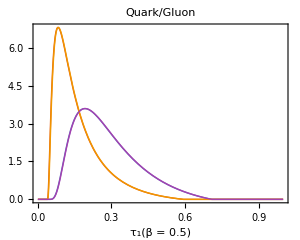
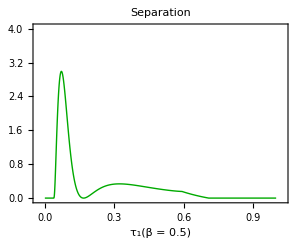

```mathematica
beta = 0.5;
QGClassifierSeparation["parton", "baseline", beta]
{
Plot[{
AngularitiesDifferentialInterpolation["parton", "baseline","quark",beta][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",beta][τ1],
AngularitiesDifferentialInterpolation["quasi-parton", "baseline","quark",beta][τ1],
AngularitiesDifferentialInterpolation["quasi-parton", "baseline","gluon",beta][τ1]
},{τ1,0,τ1max},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
,
Plot[{
(AngularitiesDifferentialInterpolation["parton", "baseline","quark",beta][τ1] - AngularitiesDifferentialInterpolation["parton", "baseline","gluon",beta][τ1])^2/(2(AngularitiesDifferentialInterpolation["parton", "baseline","quark",beta][τ1] + AngularitiesDifferentialInterpolation["parton", "baseline","gluon",beta][τ1] + 0.000000000001))},{τ1,0,τ1max},PlotLabel-> "Separation",
PlotStyle->Directive[Thick,Darker[Green]], Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8, PlotRange-> {{-0.03,1.03}, {-0.03,4.03}}]
}
```

```mathematica
{QGClassifierSeparation["parton", "baseline", 0.5],QGClassifierSeparation["parton", "baseline", 1.001],QGClassifierSeparation["parton", "baseline", 2.0]}
{QGClassifierSeparation["parton", "nogqq", 0.5],QGClassifierSeparation["parton", "nogqq", 1.001],QGClassifierSeparation["parton", "nogqq", 2.0]}
{QGClassifierSeparation["parton", "no2loop", 0.5],QGClassifierSeparation["parton", "no2loop", 1.001],QGClassifierSeparation["parton", "no2loop", 2.0]}
```

{0.267174,0.212053,0.17994}

{0.203751,0.171449,0.155041}

{0.279848,0.220787,0.186872}

```mathematica
beta = 0.5
(* Q sweep *)
{QGClassifierSeparation["parton", "Q=50", beta],
QGClassifierSeparation["parton", "Q=100", beta],
QGClassifierSeparation["parton", "Q=200", beta],
QGClassifierSeparation["parton", "Q=400", beta],
QGClassifierSeparation["parton", "Q=800", beta]}

(* R sweep *)
{QGClassifierSeparation["parton", "R=0.2", beta],
QGClassifierSeparation["parton", "R=0.4", beta],
QGClassifierSeparation["parton", "R=0.6", beta],
QGClassifierSeparation["parton", "R=0.8", beta],
QGClassifierSeparation["parton", "R=1.0", beta]}

(* αs sweep *)
{QGClassifierSeparation["parton", "α/α0=0.8", beta],
QGClassifierSeparation["parton", "α/α0=0.9", beta],
QGClassifierSeparation["parton", "α/α0=1.0", beta],
QGClassifierSeparation["parton", "α/α0=1.1", beta],
QGClassifierSeparation["parton", "α/α0=1.2", beta]}
```

0.5

{0.28832,0.277076,0.267174,0.258413,0.250623}

{0.283476,0.272816,0.267174,0.26341,0.260617}

{0.247724,0.257874,0.267174,0.275697,0.283516}

### Basic Hadronic Distributions

{0.267174,0.261462}

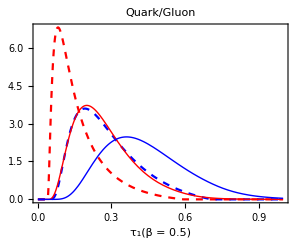
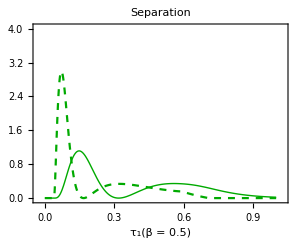

```mathematica
beta = 0.5;
{QGClassifierSeparation["parton", "baseline", beta],QGClassifierSeparation["hadron", "baseline", beta]}
{
Plot[{AngularitiesDifferentialInterpolation["parton", "baseline","quark",beta][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",beta][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",beta][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",beta][τ1]
},{τ1,0,τ1max},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->{Directive[Dashed, Red],Directive[Dashed, Blue],Directive[Thick, Red],Directive[Thick, Blue]}, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
,
Plot[{(AngularitiesDifferentialInterpolation["parton", "baseline","quark",beta][τ1] - AngularitiesDifferentialInterpolation["parton", "baseline","gluon",beta][τ1])^2/(2(AngularitiesDifferentialInterpolation["parton", "baseline","quark",beta][τ1] + AngularitiesDifferentialInterpolation["parton", "baseline","gluon",beta][τ1] + 0.000000000001)),
(AngularitiesDifferentialInterpolation["hadron", "baseline","quark",beta][τ1] - AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",beta][τ1])^2/(2(AngularitiesDifferentialInterpolation["hadron", "baseline","quark",beta][τ1] + AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",beta][τ1] + 0.000000000001))},{τ1,0,τ1max},PlotLabel-> "Separation",
PlotStyle->{Directive[Dashed,Darker[Green]],Directive[Thick,Darker[Green]]}, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8, PlotRange-> {{-0.03,1.03}, {-0.03,4.03}}]
}
```

```mathematica
{QGClassifierSeparation["hadron", "baseline", 0.5],QGClassifierSeparation["hadron", "baseline", 1.001],QGClassifierSeparation["hadron", "baseline", 2.0]}
{QGClassifierSeparation["hadron", "nogqq", 0.5],QGClassifierSeparation["hadron", "nogqq", 1.001],QGClassifierSeparation["hadron", "nogqq", 2.0]}
{QGClassifierSeparation["hadron", "no2loop", 0.5],QGClassifierSeparation["hadron", "no2loop", 1.001],QGClassifierSeparation["hadron", "no2loop", 2.0]}
```

{0.261462,0.270241,0.222948}

{0.204274,0.229604,0.199804}

{0.268501,0.279803,0.232972}

```mathematica
beta = 0.5;
(* Q sweep *)
{QGClassifierSeparation["hadron", "Q=50", beta],
QGClassifierSeparation["hadron", "Q=100", beta],
QGClassifierSeparation["hadron", "Q=200", beta],
QGClassifierSeparation["hadron", "Q=400", beta],
QGClassifierSeparation["hadron", "Q=800", beta]}

(* R sweep *)
{QGClassifierSeparation["hadron", "R=0.2", beta],
QGClassifierSeparation["hadron", "R=0.4", beta],
QGClassifierSeparation["hadron", "R=0.6", beta],
QGClassifierSeparation["hadron", "R=0.8", beta],
QGClassifierSeparation["hadron", "R=1.0", beta]}

(* αs sweep *)
{QGClassifierSeparation["hadron", "α/α0=0.8", beta],
QGClassifierSeparation["hadron", "α/α0=0.9", beta],
QGClassifierSeparation["hadron", "α/α0=1.0", beta],
QGClassifierSeparation["hadron", "α/α0=1.1", beta],
QGClassifierSeparation["hadron", "α/α0=1.2", beta]}
```

{0.190796,0.236555,0.261462,0.270892,0.272132}

{0.278152,0.267543,0.261462,0.257235,0.254014}

{0.238224,0.25078,0.261462,0.270527,0.278189}